# -Graphics-

# Finite Element Programming with the Wolfram Language

-Graphics--Graphics-

## M. K. AbdElrahman

## Wolfram Research

## Outline

### Introduction

### Finite Element Data within NDSolve

### Passing Finite Element Options to NDSolve

### A Workflow Overview

### The Partial Differential Equation Problem Setup

### Stationary PDEs

## Introduction

NDSolve provides a high-level, one-step interface for solving partial differential equations with the finite element method. However, you may want to control the steps of the solution process with more detail. The NDSolve`Fem` package provides a lower-level interface that gives extensive control for each part of the solution process.

To use the finite element functions, the package needs to be loaded.

```mathematica
Needs["NDSolve`FEM`"]
```

The low-level functions in the NDSolve`Fem` package may be used for a variety of purposes:

To better understand what NDSolve does internally and how it finds solutions

To better understand what options are available, what their usages are and when they are beneficial

To intercept the solution process at various stages and provide access to intermediate data

To enable development of specific, finite element–based solvers, not only to solve PDEs but also other areas of numerics

To use NDSolve as an equation preprocessor

### Finite Element Data within NDSolve

Set up the NDSolve`StateData object:

```mathematica
{state}=NDSolve`ProcessEquations[{Laplacian[u[x,y],{x,y}]==1,DirichletCondition[u[x,y]==0,True]}, u, {x,0,1},{y,0,1}]
```

{NDSolve`StateData[<SteadyState>]}

```mathematica
femdata=state["FiniteElementData"]
```

FiniteElementData[<1281>]

Compute the system solution:

```mathematica
NDSolve`Iterate[state]
```

The solution is then stored in the finite element data object:

```mathematica
state["SolutionData"]
```

{{None,NumericalRegion[ImplicitRegion[0≤x≤1&&0≤y≤1,{x,y}],{{0,1},{0,1}}],{-1.,-1.,-1.,-1.,-1.,-0.25,-0.25,-0.25,-0.25,-0.25,-0.90625,-0.75,-0.53125,-0.90625,-0.75,-0.53125,-0.835938,-0.648438,-0.62625,-0.90625,-0.701172,-0.648438,-0.591797,-1.,-0.960938,-0.960938,-0.794922,-0.873047,-0.835938,-0.935547,-0.398438,-0.466797,-0.873047,-0.960938,-0.935547,-0.398438,-0.58,-0.453438,-0.960938,-1.,-0.960938,-0.960938,-1.,-0.466797,-0.25,-1.,-0.25,-0.453438,-0.398438,-0.25,-0.637422,-0.835938,-0.78625,-0.690938,-0.740547,-0.835938,-0.90625,-0.25,-0.398438,-0.75,-0.648438},{},{},{},{},{}}}

Extract the solution as an InterpolatingFunction and plot the result:

```mathematica
u/.NDSolve`ProcessSolutions[state]
```

InterpolatingFunction[…]

```mathematica
Plot3D[%[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

## Passing Finite Element Options to NDSolve

Call NDSolve with finite element options specified:

```mathematica
NDSolve[{Laplacian[u[x,y],{x,y}]==1,DirichletCondition[u[x,y]==0,True]}, u, {x,0,1},{y,0,1},
Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.1},
"IntegrationOrder"->5}}]
```

{{u→InterpolatingFunction[…]}}

Solve a transient PDE with NDSolve and finite element options specified:

```mathematica
NDSolve[{D[u[t,x],t]-Laplacian[u[t,x],{x}]==t,DirichletCondition[u[t,x]==0,True],u[0,x]==0}, u, {t,0,1},{x,0,1},
Method->{
"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement",
"MeshOptions"->{"MaxCellMeasure"->0.1},"IntegrationOrder"->5}}}]
```

{{u→InterpolatingFunction[…]}}

## A Workflow Overview

The solution is found in three stages:

Initialization

Discretization

Solving

### Initialization

During the initialization stage, the PDE and boundary conditions are analyzed and classified into different components, and these results are stored in the PDECoefficientData and BoundaryConditionData objects, respectively. The finite element method data is set up and stored in the FEMMethodData object.

### Discretization

In the second stage, the PDE and boundary conditions are discretized and stored in DiscretizedPDEData and DiscretizedBoundaryConditionData. "Discretized" essentially means that the continuous PDE and boundary conditions are approximated by discrete versions represented by so-called system matrices.

### Solving

The last step is then to merge the discretized PDE with the discretized boundary conditions (DeployBoundaryCoditions) and to use LinearSolve to solve the equations.

Once the solution is found, InterpolatingFunction objects can be constructed.

## The Partial Differential Equation Problem Setup

To make a PDE susceptible to being solved by a numerical method such as the finite element method, three components are needed:

A partial differential equation (PDE)

A region

Boundary conditions

Specify a partial differential equation operator:

```mathematica
op=Laplacian[u[x,y],{x,y}]-1
```

-1+u^(0,2)[x,y]+u^(2,0)[x,y]

Create a region:

```mathematica
Ω=ImplicitRegion[0≤x≤1&&0≤y≤1,{x,y}]
```

ImplicitRegion[0≤x≤1&&0≤y≤1,{x,y}]

Set up boundary conditions at the left- and right-hand sides of the domain:

```mathematica
Subscript[Γ, D]=DirichletCondition[u[x,y]==-1,x==0]
```

DirichletCondition[u[x,y]==-1,x==0]

```mathematica
Subscript[Γ, N]=NeumannValue[-1+u[x,y],x==1]
```

NeumannValue[-1+u[x,y],x==1]

Use NDSolve to Solve the PDE

```mathematica
NDSolve[{op==Subscript[Γ, N],Subscript[Γ, D]},u,{x,y}∈Ω]
```

{{u→InterpolatingFunction[…]}}

### Use NDSolve`FEM` Functions

Extract the NDSolve`StateData object:

```mathematica
{state}=NDSolve`ProcessEquations[{op==Subscript[Γ, N],Subscript[Γ, D]},u,{x,y}x==1∈Ω,Method->{"PDEDiscretization"->"FiniteElement"}]
```

{NDSolve`StateData[<SteadyState>]}

Get the finite element data:

```mathematica
femdata=state["FiniteElementData"]
```

FiniteElementData[<1265>]

Inspect the properties:

```mathematica
femdata["Properties"]
```

{BoundaryConditionData,FEMMethodData,PDECoefficientData,Properties}

The PDECoefficientData has been created by a call to InitializePDECoefficients. The BoundaryConditionData has been created by a call to InitializeBoundaryConditions, and the FEMMethodData has been created by a call to InitializePDEMethodData. These data objects hold data for subsequent computations. The creation of these data objects is discussed in the next section.

## Stationary PDEs

### Manual Initialization

#### Variable and solution data

Create the variable data with dependent and independent variable names:

```mathematica
vd=NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y}}]
```

{None,{x,y},{u},{},{},{},{},{}}

Specify a NumericalRegion:

```mathematica
nr=ToNumericalRegion[Ω]
```

NumericalRegion[ImplicitRegion[0≤x≤1&&0≤y≤1,{x,y}],{{0,1},{0,1}}]

Create the solution data with the "Space" component set:

```mathematica
sd=NDSolve`SolutionData[{"Space"->nr}]
```

{None,NumericalRegion[ImplicitRegion[0≤x≤1&&0≤y≤1,{x,y}],{{0,1},{0,1}}],{},{},{},{},{},{}}

## Stationary PDEs

### Manual Initialization

#### InitializePDECoefficients

The coefficients of the model PDE:

```mathematica
op
```

-1+u^(0,2)[x,y]+u^(2,0)[x,y]

```mathematica
coefficients={"DiffusionCoefficients"->{{IdentityMatrix[2]}},"LoadCoefficients"->{{1}}}
```

{DiffusionCoefficients→{{{{1,0},{0,1}}}},LoadCoefficients→{{1}}}

Initialize the partial differential equation coefficients:

```mathematica
initCoeffs=InitializePDECoefficients[vd,sd,coefficients]
```

PDECoefficientData[<1,2>]

Extract the system size and the spatial dimension of the initialized coefficients:

```mathematica
{initCoeffs["SystemSize"],initCoeffs["SpatialDimension"]}
```

{1,2}

Extract the raw coefficients:

```mathematica
initCoeffs["All"]
```

{{{{1}},{{{{0},{0}}}}},{{{{{-1,0},{0,-1}}}},{{{{0},{0}}}},{{{{0,0}}}},{{0}}},{{{0}}},{{{0}}}}

During the initialization, the coefficients are classified into different categories of coefficients, such as stationary coefficients and transient coefficients:

```mathematica
initCoeffs["Properties"]
```

{All,ConservativeConvectionCoefficients,Constraints,ConvectionCoefficients,DampingCoefficients,DiffusionCoefficients,Discrete,DomainType,IndexedDiscrete,LoadCoefficients,LoadDerivativeCoefficients,MassCoefficients,MessageHead,Nonlinear,Parametric,Properties,ReactionCoefficients,SpatialDimension,Stationary,SystemSize,Transient}

## Stationary PDEs

### Manual Initialization

#### InitializeBoundaryConditions

```mathematica
initBCs=InitializeBoundaryConditions[vd,sd,{{Subscript[Γ, D],Subscript[Γ, N]}}]
```

BoundaryConditionData[<1,2>]

Boundary condition coefficients are classified into categories similar to the PDE coefficients:

```mathematica
initBCs["Properties"]
```

{All,BoundaryTolerance,Constraints,Discrete,DomainType,IndexedDiscrete,Nonlinear,Parametric,Properties,ScaleFactor,Stationary,Transient}

## Stationary PDEs

### Manual Initialization

#### InitializePDEMethodData

Initialize the finite element data with the variable and solution data:

```mathematica
methodData=InitializePDEMethodData[vd,sd]
```

FEMMethodData[<1265,{2},4>]

Query degrees of freedom, interpolation order and integration order:

```mathematica
{methodData["DegreesOfFreedom"], methodData["InterpolationOrder"], methodData["IntegrationOrder"]}
```

{1265,{2},4}

Initialize the finite element data with the variable and solution data, with options for the mesh generation:

```mathematica
methodData=InitializePDEMethodData[vd,sd,Method->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.1}}]
```

FEMMethodData[<61,{2},4>]

Query degrees of freedom, interpolation order and integration order:

```mathematica
{methodData["DegreesOfFreedom"], methodData["InterpolationOrder"], methodData["IntegrationOrder"]}
```

{61,{2},4}

During the method initialization, an ElementMesh object will be generated and stored in the NumericalRegion object:

```mathematica
mesh=nr["ElementMesh"]
```

ElementMesh[{{0.,1.},{0.,1.}},{TriangleElement[<22>]}]

For one dependent variable, the degrees of freedom correspond to the number of coordinates in the mesh:

```mathematica
Length[mesh["Coordinates"]]===methodData["DegreesOfFreedom"]
```

True

Increase the integration order:

```mathematica
InitializePDEMethodData[vd,sd,Method->{"FiniteElement","IntegrationOrder"->5}]["IntegrationOrder"]
```

5

Inspect that the state object created through NDSolve`ProcessEquations generates the same FEMMethodData object:

```mathematica
{s1}=NDSolve`ProcessEquations[{op==Subscript[Γ, N],Subscript[Γ, D]},u,{x,y}∈Ω,Method->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.1}}];
```

```mathematica
s1["FiniteElementData"]["FEMMethodData"]===methodData
```

True

## Stationary PDEs

### Extracting the Initialized Finite Element Data from NDSolve`StateData

As an alternative to the manual initialization of the finite element method data, PDE coefficients and boundary conditions, NDSolve`ProcessEquations can be utilized for this purpose:

```mathematica
{state}=NDSolve`ProcessEquations[{op==Subscript[Γ, N],Subscript[Γ, D]},u,{x,y}∈nr,Method->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.1}}];
femdata=state["FiniteElementData"]
```

FiniteElementData[<61>]

Inspect that the objects created are the same:

```mathematica
femdata["FEMMethodData"]===methodData
```

True

## Stationary PDEs

### Discretization

#### DiscretizePDE

```mathematica
discretePDE=DiscretizePDE[initCoeffs,methodData,sd]
```

DiscretizedPDEData[<61>]

The display form of the DiscretizedPDEData shows the first dimension of the system matrices:

```mathematica
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

Visualize the stiffness matrix:

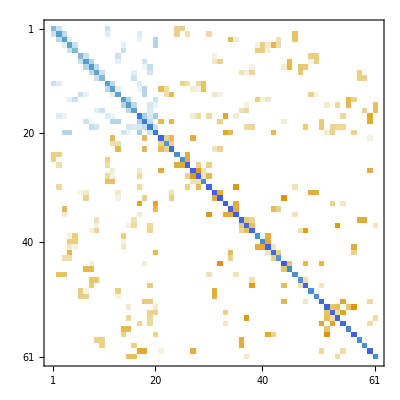

```mathematica
MatrixPlot[stiffness]
```

Extract the system matrices separately:

```mathematica
{discretePDE["LoadVector"],discretePDE["StiffnessMatrix"],discretePDE["DampingMatrix"],discretePDE["MassMatrix"]}
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

## Stationary PDEs

### Discretization

#### DiscretizeBoundaryCondition

DiscretizeBoundaryConditions computes a discretized version of the boundary conditions given. In a later step, the discretized boundary conditions are then deployed into the actual system matrices:

```mathematica
discreteBCs=DiscretizeBoundaryConditions[initBCs,methodData,sd]
```

DiscretizedBoundaryConditionData[<61>]

Components from the generalized Neumann boundary value:

```mathematica
{discreteBCs["LoadVector"], discreteBCs["StiffnessMatrix"]}
```

{SparseArray[…],SparseArray[…]}

Components from the DirichletCondition boundary condition:

```mathematica
{discreteBCs["DirichletMatrix"], discreteBCs["DirichletValues"]}
```

{SparseArray[…],SparseArray[…]}

## Stationary PDEs

### Solution

#### DeployBoundaryConditions

To have the discretized boundary conditions take effect, they need to be deployed into the system matrices. To save memory, this is done in place; no new matrices are generated:

```mathematica
DeployBoundaryConditions[{load,stiffness},discreteBCs]
```

DeployedBoundaryConditionData[<Insert>]

During the deployment of the boundary conditions, the contributions from NeumannValue are added to the stiffness and load matrix. Then the system matrices are modified such that the DirichletCondition is satisfied.

After the boundary condition deployment, the system matrices have changed; the system matrices typically contain fewer elements:

```mathematica
{load,stiffness}
```

{SparseArray[…],SparseArray[…]}

Components from the DirichletCondition boundary condition:

```mathematica
{discreteBCs["DirichletMatrix"], discreteBCs["DirichletValues"]}
```

{SparseArray[…],SparseArray[…]}

## Stationary PDEs

### Equation Solving

The system of equations can then be solved with LinearSolve:

```mathematica
Short[solution=LinearSolve[stiffness,load]]
```

{{-1.},{-1.},{-1.},{-1.},{-1.},{-0.25},«50»,{-0.90625},{-0.25},{-0.398438},{-0.75},{-0.648438}}

## Stationary PDEs

### Post-processing

As a post-processing step, an interpolation function can be created from the solution obtained from LinearSolve. For this, the solution data is updated with the solution found and ProcessPDESolutions then constructs the InterpolatingFunction:

```mathematica
NDSolve`SetSolutionDataComponent[sd,"DependentVariables",Flatten[solution]];
```

```mathematica
{ifun}=ProcessPDESolutions[methodData, sd]
```

{InterpolatingFunction[…]}

ProcessPDESolutions has the advantage that it also works well for multiple dependent variables. In the specific case at hand, an alternative to ProcessPDESolutions is to create the interpolation function directly with ElementMeshInterpolation. Here the first argument is the mesh and the second argument is the values at the mesh nodes:

```mathematica
ifun=ElementMeshInterpolation[mesh, solution]
```

InterpolatingFunction[…]

```mathematica
Plot3D[ifun[x, y],{x,y}∈mesh]
```

-Graphics3D-

It is also possible to extract the ElementMesh from the interpolating function:

```mathematica
ifun["ElementMesh"]
```

ElementMesh[{{0.,1.},{0.,1.}},{TriangleElement[<22>]}]